# 3D Design Techniques

Math 250 - Math with Mathematica
Christopher Hanusa

## Algorithmic Art

Algorithmic art is art that is created using algorithms.  You tell the computer what you want to do and the computer generates your art.  Your skills in Mathematica will allow you to create amazing intricate art.

First create a function that inputs a 3D center of a torus, its outer radius, and its inner radius, like we discussed in a previous tutorial.

```mathematica
Remove[torus]
```

```mathematica
torus[center_,outerradius_,innerradius_]:=
ParametricPlot3D[{
(outerradius+innerradius Cos[v]) Cos[u],
(outerradius+innerradius Cos[v]) Sin[u],
innerradius Sin[v]}+center,
{u,0,2 Pi},{v,0,2 Pi},Mesh->None,PlotPoints->50]
```

Now try it out to create two overlapping tori.

```mathematica
Show[
{torus[{0,0,0},1,.1],
torus[{1,0,0},1,.1]},
PlotRange->All]
```

Now use a Table command to create more overlapping tori:

```mathematica
centers=Table[{i,0,0},{i,0,10}]
```

```mathematica
Show[Map[torus[#,1,.1]&,centers],
PlotRange->All]
```

## Adding Randomness

To incorporate randomness, use RandomInteger or RandomReal. In both cases, the first input gives the range in which to choose the random number; a second input tells how many of such numbers to make, if more than one is desired.

```mathematica
RandomInteger[{-4,4}]
RandomInteger[{1,10},40]
```

You can even specify that you would like tuples of numbers.  Here we have random (x,y) coordinates with both x and y in the range [0,1].

```mathematica
RandomReal[0.5]
RandomReal[{0,1},{10,2}]
```

Here we simulate 400 rolls of a die:

```mathematica
rolls=RandomInteger[{1,6},400];
Sort[Tally[rolls]]
Histogram[rolls]
```

## Example: Generative Art

Let’s merge these last two ideas to create generative art, which is algorithmic art including aspects of randomness

```mathematica
randomcenters=RandomReal[{0,1},{10,3}]
```

```mathematica
Show[Map[torus[#,1,.1]&,randomcenters],
PlotRange->All,BoxRatios->Automatic]
```

```mathematica
randomcenters=Table[{RandomReal[{0,10}],RandomReal[{0,10}],0},{i,40}];
```

```mathematica
Show[Map[torus[#,1,.1]&,randomcenters],
PlotRange->All]
```

If you want to be able to recreate a particular instance of your work, then you need to save the initializing data.

```mathematica
randomtori=Table[torus[{RandomReal[{0,3}],RandomReal[{0,3}],0},RandomReal[{.7,1}],RandomReal[{.1,.2}]],{i,20}];
Show[randomtori,PlotRange->All]
```

I’ve written a blog post using this procedure to create some generative jewelry.

## Example: Interpolation Surfaces

An interpolation between two curves is surface that smoothly varies between the curves.

Consider the two curves f=0 and g=sine as the dependent variable changes between 0 and 2π:

```mathematica
Plot[{0,Sin[x]},{x,0,2Pi},Axes->False]
```

We are going to create a surface that slowly changes from the first function to the second, like in this Manipulate command:

```mathematica
Animate[Plot[{t Sin[x]},{x,0,2Pi},Axes->False,PlotRange->{-1,1}],{t,0,1}]
```

One simple interpolation is a linear interpolation, where at t=0 we have f and at t=1 we have g, and anywhere along the curve you have a linear combination of those two curves: (1-t)*f+t*g.  (Note what happens when you plug in x=0 and x=1.)

```mathematica
Plot[(1-t)1+(t)5,{t,0,1},PlotRange->{{0,1},{0,6}}]
```

When we do this with functions of x, we get a surface.

```mathematica
Plot3D[(1-t)0+(t) Sin[x],{t,0,1},{x,0,2Pi},BoxRatios->Automatic]
```

I suggest we make t range from 0 to 5 instead so that the surface has a less steep incline.  This is a simple transformation of the t variable---we need to replace t by t/5.

```mathematica
Plot3D[(1-t/5)0+(t/5) Sin[x],{t,0,5},{x,0,2Pi},BoxRatios->Automatic]
```

We can then extrude it.

```mathematica
Plot3D[(1-t/5)0+(t/5) Sin[x],{t,0,5},{x,0,2Pi},Extrusion->.1,BoxRatios->Automatic]
```

The extrusion is always perpendicular to the tangent plane.

Pro Tip: Instead of a linear interpolation, Smooth out your function by using a Haversine function which has horizontal tangent lines at its endpoints.  (Thanks to Clayton Shonkwiler‏ @shonk) Compare the two functions below:

```mathematica
Plot[{t,Haversine[Pi t]},{t,0,1}]
```

Here is a Haversine interpolation between 1 and 5

```mathematica
Plot[(1-Haversine[Pi t])1+(Haversine[Pi t])5,{t,0,1},PlotRange->{{0,1},{0,6}}]
```

And here is a Haversine interpolation between our two curves.

```mathematica
Plot3D[(1-Haversine[Pi t/5])0+(Haversine[Pi t/5])Sin[x],{t,0,5},{x,-5,5},Extrusion->.1,PlotPoints->50]
```

## Example: Creating a name plate

Here we create a plaque that has a raised image on it.  We first need to discretize the shape of the background:

```mathematica
shape=DiscretizeGraphics[Graphics[Rectangle[{0,0},{2,1}]]];
```

And then we discretize the image.

```mathematica
image=-Graphics-;
```

Here we resize the background shape and the image so that they fit inside one another.
We also make sure that these resized meshes are translated to have the same center.  (Use a TransformedRegion command involving a TranslationTransform)
They are showed together to make sure that the sizes and alignment are correct.

```mathematica
resizedShape=RegionResize[shape,2.5];
resizedImage=RegionResize[image,1];
translatedShape=TransformedRegion[resizedShape,TranslationTransform[-Map[Mean,RegionBounds[resizedShape]]]];
translatedImage=TransformedRegion[resizedImage,TranslationTransform[-Map[Mean,RegionBounds[resizedImage]]]];
Show[translatedShape,translatedImage]
```

Now we need to remove the image to create the flat layer that is the middle of the plate.

```mathematica
background=translatedShape;
foreground=translatedImage;
middle=BoundaryDiscretizeRegion[RegionDifference[background,foreground]]
```

The RegionBoundary command takes the boundary lines of the 2D shape:

```mathematica
outerboundary=RegionBoundary[background]
innerboundary=RegionBoundary[foreground]
```

Last, we use the RegionProduct command to add three-dimensionality to the nameplate.

```mathematica
nameplate=Show[{
RegionProduct[background,Point[{{0.}}]],
RegionProduct[outerboundary,Line[{{0.},{.1}}]],
RegionProduct[middle,Point[{{.1}}]],
RegionProduct[innerboundary,Line[{{.1},{.2}}]],
RegionProduct[foreground,Point[{{.2}}]]
}]
```

```mathematica
Export[NotebookDirectory[]<>"nameplate.stl",nameplate]
```

## Example: Costa Rica Pendant

This is an example in which the geography of Costa Rica is transformed into a polygon, and then given some thickness by adding in rectangles along the boundary to connect two polygonal sheets distance 0.25 apart.

```mathematica
CREdges=CountryData[Entity["Country","CostaRica"],"Polygon"][[1,1,1]];
```

```mathematica
Graphics3D[{Polygon[Map[Prepend[#,0]&,CREdges]],Polygon[Map[Prepend[#,0.25]&,CREdges]]}]
```

```mathematica
Graphics3D[{Table[Polygon[{
Prepend[CREdges[[i]],0],
Prepend[CREdges[[Mod[i+1,Length[CREdges],1]]],0],
Prepend[CREdges[[Mod[i+1,Length[CREdges],1]]],0.25],
Prepend[CREdges[[i]],0.25]}],{i,Length[CREdges]}]}]
```

## Example: ParametricPlot3D for a pendant

Here is the code I used to create my Polaris Pendant, which is made up of parabolas.  You can see that I first created a 2D version of the design, so that I could determine the correct functions that I wanted to include.

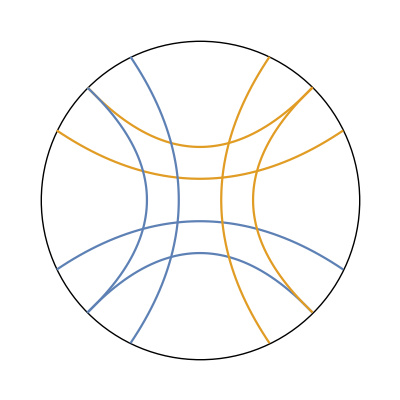

```mathematica
Show[{Graphics[Circle[{1.25,1.25},.75]],
ParametricPlot[{{t,1-(t-1.25)^2},{t,1.5+(t-1.25)^2}},{t,0.7201166105600068,1.7798833894399924}],
ParametricPlot[{{t,1.15-1/2(t-1.25)^2},{t,1.35+1/2(t-1.25)^2}},{t,0.5753270351715947,1.924672964828405}],
ParametricPlot[{{1-(u-1.25)^2,u},{1.5+(u-1.25)^2,u}},{u,0.7201166105600068,1.7798833894399924}],
ParametricPlot[{{1.15-1/2(u-1.25)^2,u},{1.35+1/2(u-1.25)^2,u}},{u,0.5753270351715947,1.924672964828405}]
},PlotRange->{{.48,2.02},{.48,2.02}}]
```

Then I converted each of the 2D ParametricPlot functions to 3D ParametricPlot3D functions.

```mathematica
pendant=Show[{
ParametricPlot3D[{.75Cos[t]+1.25,.75Sin[t]+1.25,0},{t,0,2Pi},PlotStyle->Tube[.04,PlotPoints->50]],
ParametricPlot3D[{{t,1-(t-1.25)^2,0},{t,1.5+(t-1.25)^2,0}},{t,0.7201166105600068,1.7798833894399924},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{t,1.15-1/2(t-1.25)^2,0},{t,1.35+1/2(t-1.25)^2,0}},{t,0.5753270351715947,1.924672964828405},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{1-(u-1.25)^2,u,0},{1.5+(u-1.25)^2,u,0}},{u,0.7201166105600068,1.7798833894399924},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{1.15-1/2(u-1.25)^2,u,0},{1.35+1/2(u-1.25)^2,u,0}},{u,0.5753270351715947,1.924672964828405},PlotStyle->Tube[.03,PlotPoints->50]]
},PlotRange->{{.48,2.02},{.48,2.02},{-.2,.2}}]
```

-Graphics3D-